```mathematica
νp=({{1, 1, 3}, {0, 0, 0}});
νr=({{0, 0, 2}, {0, 1, 1}});
S=(νp-νr);S//MatrixForm
```

(1 | 1 | 1
0 | -1 | -1)

```mathematica
MM = MatrixRank[S];
CL = Transpose@NullSpace[Transpose@S];
CC = NullSpace[S];
$Assumptions=β>1;
{NN,RR} = Dimensions[S];
SubPlus[λ][ρ_] :=SubPlus[k][ρ]Product[x[i]^νr[[i,ρ]],{i,1,NN}];SubMinus[λ][ρ_]:=SubMinus[k][ρ]Product[x[i]^νp[[i,ρ]],{i,1,NN}];
rates = {SubPlus[k][1]->1,SubMinus[k][1]->1,SubPlus[k][2]->1,SubMinus[k][2]->β,SubPlus[k][3]->μ,SubMinus[k][3]->μ α}/.μ->3
J =Table[SubPlus[λ][ρ]- SubMinus[λ][ρ],{ρ,1,RR}];
J /.rates//MatrixForm
```

{k_+[1]→1,k_-[1]→1,k_+[2]→1,k_-[2]→β,k_+[3]→3,k_-[3]→3 α}

(1-x[1]
-β x[1]+x[2]
-3 α x[1]^3+3 x[1]^2 x[2])

```mathematica
A= S.J;A/.rates //MatrixForm
```

(1-x[1]-β x[1]-3 α x[1]^3+x[2]+3 x[1]^2 x[2]
β x[1]+3 α x[1]^3-x[2]-3 x[1]^2 x[2])

```mathematica
SubStar[x]= Simplify@SolveValues[A == 0, Table[x[i],{i,1,NN}]][[1]]/.rates
```

{1,1/4 (3 α+β)}

```mathematica
shift={x[1]->Δx[1]+SubStar[x][[1]],x[2]->Δx[2]+SubStar[x][[2]]}
```

{x[1]→1+Δx[1],x[2]→1/4 (3 α+β)+Δx[2]}

```mathematica
Subscript[A, Δx] = A/.rates/.shift //FullSimplify
```

{4 Δx[2]+1/4 Δx[1] (-4+β (2+3 Δx[1])-3 α (6+Δx[1] (9+4 Δx[1]))+12 (2+Δx[1]) Δx[2]),1/4 (-β Δx[1] (2+3 Δx[1])+3 α Δx[1] (6+Δx[1] (9+4 Δx[1]))-4 (4+3 Δx[1] (2+Δx[1])) Δx[2])}

```mathematica
Subscript[A, 1]=Grad[Subscript[A, Δx],{Δx[1],Δx[2]}]/.{Δx[1]->0,Δx[2]->0};Subscript[A, 1]//MatrixForm
```

(1/4 (-4-18 α+2 β) | 4
1/4 (18 α-2 β) | -4)

```mathematica
Subscript[α, c]=SolveValues[Tr[Subscript[A, 1]]==0,α][[1]]
```

1/9 (-10+β)

```mathematica
Subscript[A, 1]/.α->Subscript[α, c]//FullSimplify//MatrixForm
```

(4 | 4
-5 | -4)

```mathematica
Eigenvalues[Subscript[A, 1]]/.α->Subscript[α, c]//FullSimplify
```

{-2 ⅈ,2 ⅈ}

```mathematica
T=Transpose@Eigenvectors[Subscript[A, 1]]
```

{{-(-6+9 α-β+√(36+180 α+81 α^2-20 β-18 α β+β^2))/(2 (9 α-β)),-(-6+9 α-β-√(36+180 α+81 α^2-20 β-18 α β+β^2))/(2 (9 α-β))},{1,1}}

```mathematica
Inverse[T].Subscript[A, 1].T/.α->Subscript[α, c]//FullSimplify//MatrixForm
```

(-2 ⅈ | 0
0 | 2 ⅈ)

```mathematica
Subscript[M, can]={{0,-2},{2,0}};Subscript[M, can]//MatrixForm
```

(0 | -2
2 | 0)

```mathematica
flip={{0,1},{1,0}};flip//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
U=Eigenvectors[Subscript[M, can]]
```

{{ⅈ,1},{-ⅈ,1}}

```mathematica
U.Subscript[M, can].Inverse[U]//FullSimplify//MatrixForm
```

(-2 ⅈ | 0
0 | 2 ⅈ)

```mathematica
M=Inverse[U].Inverse[T].Subscript[A, 1].T.U//FullSimplify;M//MatrixForm
```

(1/4 (-10-9 α+β) | 1/4 ⅈ √((2+9 α-β) (18+9 α-β))
-1/4 ⅈ √((2+9 α-β) (18+9 α-β)) | 1/4 (-10-9 α+β))

```mathematica
Inverse[U].Inverse[T].Subscript[A, 1].T.U/.α->Subscript[α, c]//FullSimplify//MatrixForm
```

(0 | -2
2 | 0)

```mathematica
V=T.U//FullSimplify;V//MatrixForm
```

(-(ⅈ √((2+9 α-β) (18+9 α-β)))/(9 α-β) | -1-6/(-9 α+β)
0 | 2)

```mathematica
Subscript[A, y]=Inverse[V].(Subscript[A, Δx]/.{Δx[1]->(V.{y[1],y[2]})[[1]],Δx[2]->(V.{y[1],y[2]})[[2]]});
```

```mathematica
Subscript[A, y,1]=Grad[Subscript[A, y],{y[1],y[2]}]/.{y[1]->0,y[2]->0};Subscript[A, y,1]//MatrixForm//FullSimplify
```

(1/4 (-10-9 α+β) | 1/4 ⅈ √((2+9 α-β) (18+9 α-β))
-1/4 ⅈ √((2+9 α-β) (18+9 α-β)) | 1/4 (-10-9 α+β))

```mathematica
$Assumptions=ϵ>0
```

ϵ>0

```mathematica
Subscript[A, y,ϵ]=Subscript[A, y]/.α->Subscript[α, c]-ϵ//FullSimplify
```

{1/(24 (10+9 ϵ)^3 √(-64+81 ϵ^2))(-59049 ⅈ ϵ^5 (3 y[1]^2 (-3+4 y[2])+y[2] (-6+(9-4 y[2]) y[2]))-256 (4 (-10+β) √(-64+81 ϵ^2) y[1]^3+3 √(-64+81 ϵ^2) y[1] y[2] (75+8 (-5+2 β) y[2])+12 ⅈ y[1]^2 (75+4 (-25+4 β) y[2])+4 ⅈ y[2] (375+16 (5+4 β) y[2]^2))-13122 ϵ^4 (2 √(-64+81 ϵ^2) y[1]^3-3 √(-64+81 ϵ^2) y[1] (-1+y[2]) (-1+2 y[2])-6 ⅈ y[1]^2 (18+(-24+β) y[2])+2 ⅈ y[2] (-45+y[2] (90+(-44+β) y[2])))-144 ϵ (16 (-14+β) √(-64+81 ϵ^2) y[1]^3+240 ⅈ y[1]^2 (27+4 (-9+β) y[2])+3 √(-64+81 ϵ^2) y[1] (-125+690 y[2]+8 (-53+12 β) y[2]^2)+16 ⅈ y[2] (450+y[2] (225+8 (-1+14 β) y[2])))+2916 ϵ^3 ((-14+β) √(-64+81 ϵ^2) y[1]^3+3 ⅈ y[1]^2 (87+4 (-29+5 β) y[2])-3 √(-64+81 ϵ^2) y[1] (-15+y[2] (48+(-34+β) y[2]))-ⅈ y[2] (-354+y[2] (1269+(-652+52 β) y[2])))+648 ϵ^2 (2 (6+β) √(-64+81 ϵ^2) y[1]^3+426 ⅈ y[1]^2 (-3+4 y[2])-9 √(-64+81 ϵ^2) y[1] (-25+y[2] (93+(-64+6 β) y[2]))-2 ⅈ y[2] (345+y[2] (1845+4 (-211+60 β) y[2])))),1/(24 (10+9 ϵ)^3)(4 ⅈ (10-β+9 ϵ) (-64+81 ϵ^2)^(3/2) y[1]^3+3 (-64+81 ϵ^2) y[1]^2 (3 (10+9 ϵ)^2+4 (-(10+9 ϵ)^2+β (16+9 ϵ)) y[2])+y[2] (54 ϵ (10+9 ϵ)^3-81 ϵ (10+9 ϵ)^2 (16+9 ϵ) y[2]+4 (16+9 ϵ)^2 (-4 (5+4 β)-9 (-8+β) ϵ+81 ϵ^2) y[2]^2)-6 ⅈ √(-64+81 ϵ^2) y[1] ((10+9 ϵ)^3-3 (8+9 ϵ) (10+9 ϵ)^2 y[2]+2 (16+9 ϵ) ((4+9 ϵ) (10+9 ϵ)-β (16+9 ϵ)) y[2]^2))}

```mathematica
Subscript[A, y,ϵ,1]=Grad[Subscript[A, y,ϵ],{y[1],y[2]}]/.{y[1]->0,y[2]->0};Subscript[A, y,ϵ,1]//MatrixForm//FullSimplify
```

((9 ϵ)/4 | 1/4 ⅈ √(-64+81 ϵ^2)
-1/4 ⅈ √(-64+81 ϵ^2) | (9 ϵ)/4)

```mathematica
Normal@Series[Subscript[A, y,ϵ,1],{ϵ,0,1}]
```

{{(9 ϵ)/4,-2},{2,(9 ϵ)/4}}

```mathematica
Subscript[F, δ,ϵ]=Subscript[A, y,ϵ]/.y[i_]->δx[i][t];
```

```mathematica
par = {β->19,ϵ->0.001}
```

{β→19,ϵ→0.001}

```mathematica
EQS=Table[D[δx[i][t],t]==Subscript[F, δ,ϵ][[i]],{i,1,NN}];EQS//MatrixForm
IC={δx[1][0]==10,δx[2][0]==10};
vars = Table[δx[i][t],{i,1,NN}];
```

(δx[1]'[t]==(-59049 ⅈ ϵ^5 (3 (δx[1][t])^2 (-3+4 δx[2][t])+δx[2][t] (-6+(9-4 δx[2][t]) δx[2][t]))-256 (4 (-10+β) √(-64+81 ϵ^2) (δx[1][t])^3+3 √(-64+81 ϵ^2) δx[1][t] δx[2][t] (75+8 (-5+2 β) δx[2][t])+12 ⅈ (δx[1][t])^2 (75+4 (-25+4 β) δx[2][t])+4 ⅈ δx[2][t] (375+16 (5+4 β) (δx[2][t])^2))-13122 ϵ^4 (2 √(-64+81 ϵ^2) (δx[1][t])^3-3 √(-64+81 ϵ^2) δx[1][t] (-1+δx[2][t]) (-1+2 δx[2][t])-6 ⅈ (δx[1][t])^2 (18+(-24+β) δx[2][t])+2 ⅈ δx[2][t] (-45+δx[2][t] (90+(-44+β) δx[2][t])))-144 ϵ (16 (-14+β) √(-64+81 ϵ^2) (δx[1][t])^3+240 ⅈ (δx[1][t])^2 (27+4 (-9+β) δx[2][t])+3 √(-64+81 ϵ^2) δx[1][t] (-125+690 δx[2][t]+8 (-53+12 β) (δx[2][t])^2)+16 ⅈ δx[2][t] (450+δx[2][t] (225+8 (-1+14 β) δx[2][t])))+2916 ϵ^3 ((-14+β) √(-64+81 ϵ^2) (δx[1][t])^3+3 ⅈ (δx[1][t])^2 (87+4 (-29+5 β) δx[2][t])-3 √(-64+81 ϵ^2) δx[1][t] (-15+δx[2][t] (48+(-34+β) δx[2][t]))-ⅈ δx[2][t] (-354+δx[2][t] (1269+(-652+52 β) δx[2][t])))+648 ϵ^2 (2 (6+β) √(-64+81 ϵ^2) (δx[1][t])^3+426 ⅈ (δx[1][t])^2 (-3+4 δx[2][t])-9 √(-64+81 ϵ^2) δx[1][t] (-25+δx[2][t] (93+(-64+6 β) δx[2][t]))-2 ⅈ δx[2][t] (345+δx[2][t] (1845+4 (-211+60 β) δx[2][t]))))/(24 (10+9 ϵ)^3 √(-64+81 ϵ^2))
δx[2]'[t]==(4 ⅈ (10-β+9 ϵ) (-64+81 ϵ^2)^(3/2) (δx[1][t])^3+3 (-64+81 ϵ^2) (δx[1][t])^2 (3 (10+9 ϵ)^2+4 (-(10+9 ϵ)^2+β (16+9 ϵ)) δx[2][t])+δx[2][t] (54 ϵ (10+9 ϵ)^3-81 ϵ (10+9 ϵ)^2 (16+9 ϵ) δx[2][t]+4 (16+9 ϵ)^2 (-4 (5+4 β)-9 (-8+β) ϵ+81 ϵ^2) (δx[2][t])^2)-6 ⅈ √(-64+81 ϵ^2) δx[1][t] ((10+9 ϵ)^3-3 (8+9 ϵ) (10+9 ϵ)^2 δx[2][t]+2 (16+9 ϵ) ((4+9 ϵ) (10+9 ϵ)-β (16+9 ϵ)) (δx[2][t])^2))/(24 (10+9 ϵ)^3))

```mathematica
Subscript[t, max]=1000;
sols=NDSolve[{EQS/.par,IC},vars,{t,0,Subscript[t, max]}][[1]]
```

{δx[1][t]→InterpolatingFunction[…][t],δx[2][t]→InterpolatingFunction[…][t]}

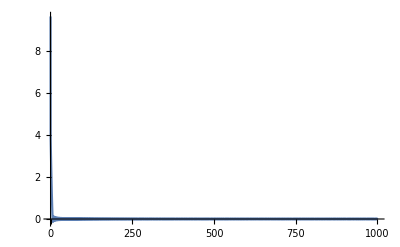

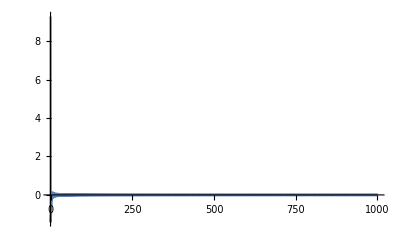

```mathematica
Plot[δx[1][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
Plot[δx[2][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
```

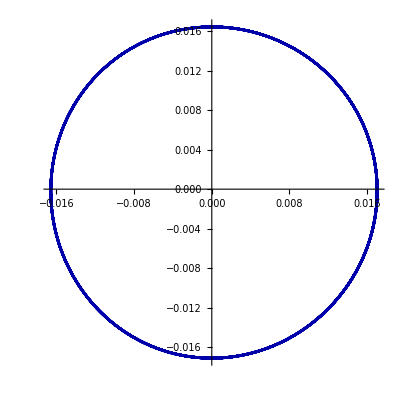

```mathematica
ParametricPlot[{δx[1][t],δx[2][t]}/.sols,{t,Subscript[t, max] 9/10,Subscript[t, max]},PlotRange->All,PlotPoints->1000,PlotStyle->Darker@Blue]
```

```mathematica
τ=10^2 Subscript[t, max];
```

```mathematica
radius1=ParametricNDSolveValue[{EQS/.{β->19},IC},Sqrt[(δx[1][t])^2+(δx[2][t])^2],{t,0,Subscript[t, max]},{ϵ}]
```

ParametricFunction[<>]

```mathematica
ll1=0.001
```

0.001

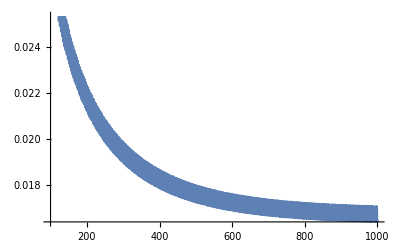

```mathematica
Plot[radius1[ll1],{t,.1 Subscript[t, max],Subscript[t, max]}]
```

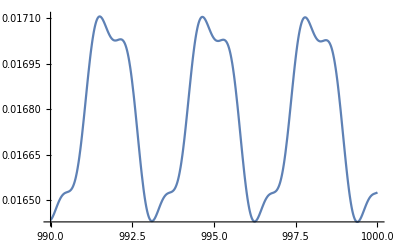

```mathematica
Plot[radius1[ll1],{t,.99 Subscript[t, max],Subscript[t, max]}]
```